# Comparing σHe-4 to Schwaller

## with no curve fitting

## Micah Buuck

9/5/13

## Glauber

The data below is pulled directly from Wallace's lecture in Advances in Nuclear Physics:

```mathematica
ppdat={{0.21,2.5-2.93 ⅈ,14.15-6.33 ⅈ},{0.21,2.42-3.11 ⅈ,15.6-7.1 ⅈ},{0.325,2.51-1.85 ⅈ,10.-10.53 ⅈ},{0.325,2.48-1.98 ⅈ,10.5-10.1 ⅈ},{0.425,2.78-1.53 ⅈ,6.68-8.73 ⅈ},{0.425,2.48-1.59 ⅈ,6.88-8.8 ⅈ},{0.515,3.24-0.74 ⅈ,4.27-3.93 ⅈ},{0.515,3.22-1.41 ⅈ,5.35-6.78 ⅈ},{0.585,3.7-1.2 ⅈ,4.83-5.48 ⅈ},{0.665,4.25-0.88 ⅈ,4.65-4.38 ⅈ},{0.73,4.63-0.61 ⅈ,4.6-3.65 ⅈ},{0.831,4.88-0.17 ⅈ,4.33-2.79 ⅈ}};
```

```mathematica
pndat={{.210,4.18-I 2.70,10-I 5.66},{.210,4.42-I 3.64,16.44-I 4.54},{.325,3.58-I 1.04,10.1-I 9.60},{.325,3.82-I 1.15,10.10-I 9.94},{.425,3.41-I 0.47,6.25-I 8.23},{.425,3.40-I 0.13,6.09-I 5.97},{.515,3.47-I 0.20,4.77-I 6.40},{.515,3.33+I 0.61,4.74-I 3.58},{.585,3.57+I 0.02,4.25-I 5.24},{.665,3.70+I 0.29,4.01-I 4.22},{.730,3.80+I 0.49,3.94-I 3.51},{.831,3.83+I 0.78,3.77-I 2.59}};
```

```mathematica
A0=(ppdat[[All,2]]+pndat[[All,2]])/2;
βA=(ppdat[[All,3]]+pndat[[All,3]])/2;
```

```mathematica
m=0.938272046;(*GeV/c^2*)
mn=1.00137842*m(*GeV/c^2*);
M=2*m+2*mn;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
σ1=A0/βA;
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
Fcm[q_]:=Exp[B*q^2/A]
EnL=ppdat[[All,1]]+m;
s=m^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-m^2];
k=P*(M/Sqrt[s]);
s2=m^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(m+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(m+M)/Sqrt[s];
```

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+βA)*Sum[Binomial[A,j]/j*(-A0/(B+βA))^j*Exp[-(B+βA)*q^2/j],{j,1,A}]*ℏc
```

The graph below shows that the fitting routine to the values provided by Wallace isn't great, since there aren't enough control points. In fact, the fit to the pdg data isn't great either, so this could possibly be improved.

```mathematica
p2En[x_]:={Sqrt[x[[1]]^2+m^2]-m,x[[2]]}
```

```mathematica
mult[x_]:={x[[1]]/1000.,x[[2]]}
```

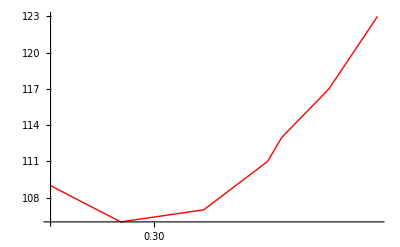

```mathematica
σHe4NLP=ListLogLinearPlot[mult/@σHe4data,PlotStyle->Red,Joined->True]
```

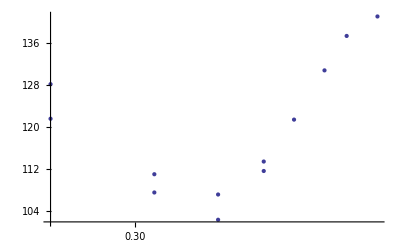

```mathematica
p1=ListLogLinearPlot[Transpose[{ppdat[[All,1]],40*Pi/(k/ℏc)*Im[F0[0]]}]]
```

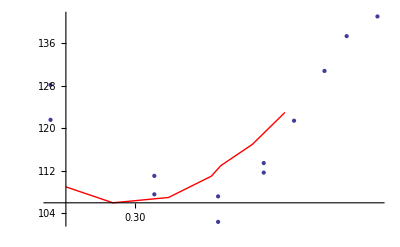

```mathematica
Show[σHe4NLP,p1,PlotRange->All]
```

The red is connected data points from the Schwaller experiment. The blue points are the Glauber approximation calculated at the energies given by Wallace in Advances in Nuclear Physics 12. You can see that the fit is not very good in the data region.

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 βA)]
```

```mathematica
Γ[0]
```

{0.314761-0.0768537 ⅈ,0.256205-0.117596 ⅈ,0.223157+0.079709 ⅈ,0.233068+0.0747904 ⅈ,0.25055+0.173962 ⅈ,0.263134+0.167038 ⅈ,0.373446+0.322754 ⅈ,0.355639+0.285869 ⅈ,0.398557+0.340588 ⅈ,0.496262+0.424694 ⅈ,0.586578+0.47774 ⅈ,0.711434+0.547841 ⅈ}

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

{-39.7022-44.8519 ⅈ,-47.0071-44.39 ⅈ,-18.3206-41.0505 ⅈ,-20.0013-42.5899 ⅈ,-11.2453-42.1315 ⅈ,-9.57705-40.1043 ⅈ,-1.64224-46.6345 ⅈ,-1.3691-45.3213 ⅈ,-2.50871-50.9634 ⅈ,4.19526-56.1798 ⅈ,9.92024-59.917 ⅈ,18.5684-61.63 ⅈ}

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]][[8]]]},{q,0.001,1.001,.1}]]
```

{{0.001,45.1348},{0.101,28.7137},{0.201,18.4459},{0.301,11.9323},{0.401,7.74451},{0.501,5.02518},{0.601,3.2514},{0.701,2.09768},{0.801,1.35655},{0.901,0.892258},{1.001,0.612428}}

```mathematica
interp1=Interpolation[{{0.001,45.13483849099055},{0.101,28.71374071377477},{0.201,18.44594838299124},{0.30100000000000005,11.932264105094443},{0.401,7.7445115019034185},{0.501,5.0251776589466255},{0.6010000000000001,3.251399267531174},{0.7010000000000001,2.0976769411059926},{0.801,1.3565514777337822},{0.901,0.8922578011512067},{1.001,0.6124282506755668}}];
```

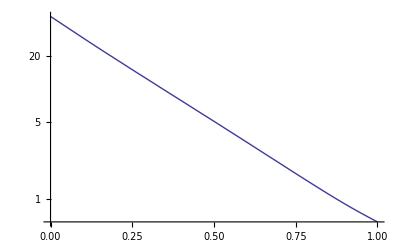

```mathematica
Quiet[LogPlot[interp1[t],{t,0,1}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]][[8]]]},{q,0.001,1.001,.1}]]
```

{{0.001,-1.59581},{0.101,-1.08458},{0.201,-0.590992},{0.301,-0.120638},{0.401,0.321036},{0.501,0.728447},{0.601,1.09519},{0.701,1.41323},{0.801,1.67276},{0.901,1.86493},{1.001,1.99086}}

```mathematica
interp2=Interpolation[{{0.001,-1.5958133921811601},{0.101,-1.084579638004722},{0.201,-0.5909924699873587},{0.30100000000000005,-0.12063849138098676},{0.401,0.3210361667087452},{0.501,0.72844705010775},{0.6010000000000001,1.095190765219551},{0.7010000000000001,1.413231860590959},{0.801,1.672762792438444},{0.901,1.8649324620912109},{1.001,1.990863668908967}}];
```

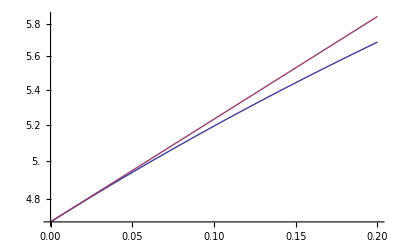

```mathematica
Quiet[LogPlot[{interp2[t]+2*Pi,Exp[t/.9+Log[interp2[0]+2*Pi]]},{t,0,.2}]]
```

The approximation of the phase as exponential in q^2 isn't as good, but is approximately correct in the region where the potential contributes. If these corrections aren't accurate enough, the other option is to use the full equation for the corrections which takes gradients of U rather than the reduced version Wallace derives by assuming U is Gaussian in q.

```mathematica
Quiet[U[.1]]
```

{-33.0752-41.8391 ⅈ,-38.1602-40.0733 ⅈ,-12.8856-38.7414 ⅈ,-14.2591-40.1801 ⅈ,-7.23685-40.4122 ⅈ,-6.24159-38.2988 ⅈ,0.735813-44.812 ⅈ,0.934222-43.305 ⅈ,0.211825-49.0198 ⅈ,6.40309-53.8866 ⅈ,11.7099-57.3747 ⅈ,19.689-59.0057 ⅈ}

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])];
```

```mathematica
Z=U[0]/(-I*4*Pi*σ1*βA);(*Unitless*)
```

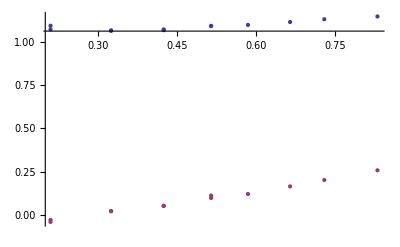

```mathematica
Show[ListPlot[Transpose[{ppdat[[All,1]],Re[Z]}]],ListPlot[Transpose[{ppdat[[All,1]],Im[Z]}],PlotStyle->ColorData[1,2]],PlotRange->All]
```

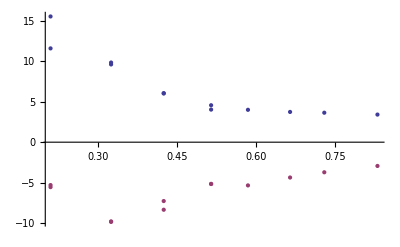

```mathematica
Show[ListPlot[Transpose[{ppdat[[All,1]],Re[γ]}]],ListPlot[Transpose[{ppdat[[All,1]],Im[γ]}],PlotStyle->ColorData[1,2]],PlotRange->All]
```

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*βA/(γ+βA)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(βA+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(βA+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(βA+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(βA*(B+γ1)))/(γ+B)+(1-γ1/βA)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(βA*(B+γ1)))*(1-γ1/βA)]]]
γ2:=γ*βA/(βA+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(βA+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(βA+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(βA*σ1*Z)^2/(2*(2*Pi*(B+βA))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*βA/(B+βA))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(βA*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*βA/(B+βA))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
mult[x_]:={x[[1]]/1000.,x[[2]]}
σHe4NLP=ListLogLinearPlot[mult/@σHe4data];
```

The corrections appear to be quite small, but it might be useful to see what things look like with more accurate fits to the scattering data.

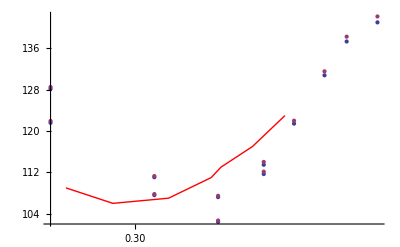

```mathematica
Show[ListLogLinearPlot[Transpose[{ppdat[[All,1]],(4*Pi)/(k/ℏc)*Im[F0[0]]*10}]],ListLogLinearPlot[Transpose[{ppdat[[All,1]],(4*Pi)/(k/ℏc)*Im[F0[0]+FO1[0]+FD1[0]]*10}],PlotStyle->ColorData[1,2]],σHe4NLP,PlotRange->All]
```

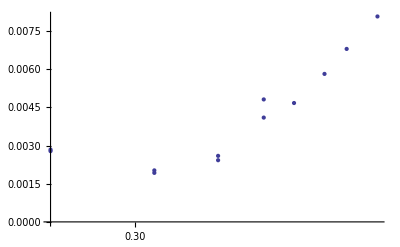

```mathematica
ListLogLinearPlot[Transpose[{ppdat[[All,1]],Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]}]]
```

The graph above is the fractional contribution the first order correction makes at each energy